```mathematica
f[t_] := UnitBox[t];
```

```mathematica
F[f_]= FourierTransform[f[t],t,f,FourierParameters->{0, -2*Pi}]
```

Sinc[f π]

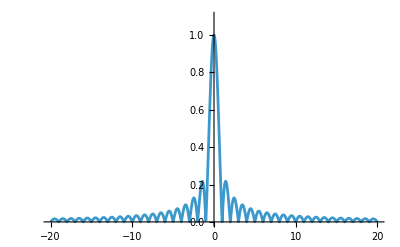

```mathematica
Plot[{Abs[F[f]]},{f,-20,20},PlotRange->{0,1.1}]
```

```mathematica
f0 = 20;
```

```mathematica
fFiltered[t_] = Integrate[F[f]*Exp[I*2Pi*f*t],{f,-f0,f0}];
```

```mathematica
f2=1;
```

```mathematica
fFiltered2[t_] = Integrate[F[f]*Exp[I*2Pi*f*t],{f,-f2,f2}];
```

```mathematica
f3=5;
```

```mathematica
fFiltered3[t_] = Integrate[F[f]*Exp[I*2Pi*f*t],{f,-f3,f3}];
```

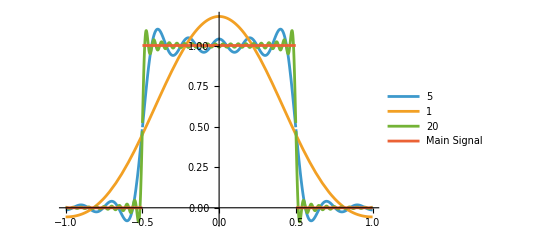

```mathematica
Plot[{fFiltered3[t],fFiltered2[t],fFiltered[t],f[t]},{t,-1,1},PlotLegends->{5,1,20,Main Signal}]
```

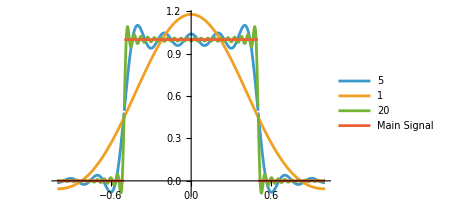

```mathematica
Equal[Integrate[Abs[F[f]]^2,{f,-Infinity,Infinity}], Integrate[Abs[f[t]]^2,{t,-Infinity,Infinity}]]
```

True

```mathematica
f0=200;
```

```mathematica
finverse[t_] = Integrate[{2F[2f]*Exp[I*2Pi*f*t]},{f,-f0,f0}];
```

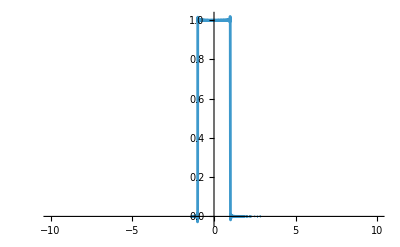

```mathematica
Plot[finverse[t],{t,-10,10},Exclusions->None]
```